## Analytical proof of saturation of Mandelstam-Tamm bound for infinitesimally short times

```mathematica
ClearAll[H];H=.;
Do[ToExpression["ClearAll[H"<>ToString[n]<>"];Unset[H"<>ToString[n]<>"]"],{n,1,10}];

Do[ToExpression["ClearAll[h"<>ToString[n]<>"];Unset[h"<>ToString[n]<>"]"],{n,1,10}];

ClearAll[ΔH];ΔH=.;
ClearAll[δt];δt=.;

Unprotect[NonCommutativeMultiply];

ClearAll[NonCommutativeMultiply];

SetAttributes[NonCommutativeMultiply,OneIdentity];

NonCommutativeMultiply[x_]:=x;

SetAttributes[NonCommutativeMultiply,Flat];

A_**(B_+C_):=A**B+A**C;
(A_+B_)**C_:=A**C+B**C;

NonCommutativeMultiply[A_,Times[B_?IsNumericQ,C__]]:=B NonCommutativeMultiply[A,Times[C]];
NonCommutativeMultiply[Times[B_?IsNumericQ,C__],A_]:=B NonCommutativeMultiply[Times[C],A];

Protect[NonCommutativeMultiply];

ClearAll[Scalar];Scalar=.;

Scalar[a_Plus,b_]:=Scalar[#,b]&/@a;
Scalar[a_,b_Plus]:=Scalar[a,#]&/@b;

Scalar[ψ,ψ]:=1;
Scalar[ψ0,ψ0]:=1;

Scalar/:MakeBoxes[Scalar[x_,y_],StandardForm]:=TemplateBox[{ToBoxes[x],ToBoxes[y]},"Scalar",DisplayFunction->(RowBox[{"⟨",RowBox[{#1,",",#2}],"⟩"}]&)]

IsHermitianQ[x_]:=False;
IsHermitianQ[H]^=True;
Do[ToExpression["IsHermitianQ[h"<>ToString[n]<>"]^=True"],{n,1,10}];

ClearAll[IsNumericQ];

IsNumericQ[δt]^=True;
IsNumericQ[ΔH]^=True;
Do[ToExpression["IsNumericQ[H"<>ToString[n]<>"]^=True"],{n,1,10}];

IsNumericQ[x_]:=NumericQ[x];

IsNumericQ[Scalar[_,_]]:=True;

IsNumericQ[Power[x_?IsNumericQ,y_?IsNumericQ]]:=True;

IsNumericQ[Plus[x_,y_]]:=IsNumericQ[x]&&IsNumericQ[y];
IsNumericQ[Times[x_,y_]]:=IsNumericQ[x]&&IsNumericQ[y]

IsRealQ[x_]:=Internal`RealValuedNumericQ[x];

IsRealQ[δt]^=True;
IsRealQ[ΔH]^=True;
Do[ToExpression["IsRealQ[H"<>ToString[n]<>"]^=True"],{n,1,10}];

IsPositiveQ[x_]:=Positive[x];
IsPositiveQ[ΔH]^=True;
IsPositiveQ[δt]^=True;

Unprotect[Conjugate];

ClearAll[Conjugate]; SetAttributes[Conjugate,{Listable,NumericFunction}];

Conjugate/:MakeBoxes[Conjugate[x_],StandardForm]:=TemplateBox[{Parenthesize[x,StandardForm,Power]},"Conjugate",DisplayFunction->(SuperscriptBox[#1,"*"]&)]

Conjugate[x_?IsRealQ]:=x;
Conjugate[Scalar[a_,b_]]:=Scalar[b,a];

Protect[Conjugate];

Unprotect[Power];

ClearAll[Power];

SetAttributes[Power,{Listable,NumericFunction,OneIdentity}];
Power[Times[-1,x_],Rational[n_,m_?EvenQ]]:=ⅈ^((2n)/m) Power[Times[x],Rational[1,2]];

Power/:Power[Power[x_?IsPositiveQ,a_],b_?IsNumericQ]:=x^(a b);

Power/:Power[Times[A__,Power[x_?IsPositiveQ,a_]],Rational[n_,m_]]/;IntegerQ[a/m]:=Power[x,a Rational[n,m]]Power[Times[A],Rational[n,m]];

IsNumericQ[Power[x_?IsNumericQ,n_?IsNumericQ]]:=True;

Protect[Power];

Scalar[a_,Times[b_?IsNumericQ,c__]]:=b Scalar[a,Times[c]];
Scalar[Times[a_?IsNumericQ,b__],c_]:=Conjugate[a] Scalar[Times[b],c];

Scalar[NonCommutativeMultiply[a_?IsHermitianQ,b_],c_]:= Scalar[b,NonCommutativeMultiply[a,c]];
Scalar[NonCommutativeMultiply[NonCommutativeMultiply[a_?IsHermitianQ,b_],c_],d_]:= Scalar[NonCommutativeMultiply[b,c],NonCommutativeMultiply[a,d]];

ψevol={ψ->Sum[(-ⅈ δt)^n/(n!)If[n≥1,NonCommutativeMultiply@@Table[H,{m,0,n-1}]**ψ0,ψ0],{n,0,4}]};

v1=(Scalar[ψ0,ψ]ψ0-Scalar[ψ,ψ0]Scalar[ψ0,ψ]ψ);
v2=-ⅈ (H**ψ-Scalar[ψ,H**ψ] ψ);


v3=Expand[1/ΔH(v2-Scalar[v1,v2]/Scalar[v1,v1] v1)];


Hmoments=Table[ψ0Module[{tmp=H},Do[tmp=H**tmp,{n,1,#-1}];tmp]&[m]**ψ0->ToExpression["H"<>ToString[m]],{m,1,10}];


Series[v3/.ψevol/.Hmoments/.H2->ΔH^2+H1^2/.δt->ϵ,{ϵ,0,1}]/.ϵ->δt

Series[Scalar[v3,v3]/.ψevol/.Hmoments/.H2->ΔH^2+H1^2/.δt->ϵ,{ϵ,0,2}]/.ϵ->δt


deltaA=√(Normal[Series[FullSimplify[Scalar[v1,v1]/.ψevol/.Hmoments/.H2->ΔH^2+H1^2]/.δt->ϵ,{ϵ,0,2}]]/.ϵ->δt)

v3=Expand[1/deltaA(v1-Scalar[v2,v1]/Scalar[v2,v2] v2)];

Series[v3/.ψevol/.Hmoments/.H2->ΔH^2+H1^2/.δt->ϵ,{ϵ,0,1}]/.ϵ->δt

Series[Scalar[v3,v3]/.ψevol/.Hmoments/.H2->ΔH^2+H1^2/.δt->ϵ,{ϵ,0,2}]/.ϵ->δt
```

((H1^4 ψ0-H1 H3 ψ0+2 H1^2 ΔH^2 ψ0+ΔH^4 ψ0-H1^3 H**ψ0+H3 H**ψ0-H1 ΔH^2 H**ψ0-ΔH^2 H**H**ψ0) δt)/(2 ΔH^3)+O[δt]^2

((-H1^6+2 H1^3 H3-H3^2-3 H1^4 ΔH^2+2 H1 H3 ΔH^2+H4 ΔH^2-3 H1^2 ΔH^4-ΔH^6) δt^2)/(4 ΔH^4)+O[δt]^3

ΔH δt

((H1^4 ψ0-H1 H3 ψ0+2 H1^2 ΔH^2 ψ0+ΔH^4 ψ0-H1^3 H**ψ0+H3 H**ψ0-H1 ΔH^2 H**ψ0-ΔH^2 H**H**ψ0) δt)/(2 ΔH^3)+O[δt]^2

((-H1^6+2 H1^3 H3-H3^2-3 H1^4 ΔH^2+2 H1 H3 ΔH^2+H4 ΔH^2-3 H1^2 ΔH^4-ΔH^6) δt^2)/(4 ΔH^4)+O[δt]^3

## Time-dependent Hamiltonians

```mathematica
ψevol={ψ->Sum[(-ⅈ δt)^n/((*n!*)1)If[n≥1,ToExpression["h"<>ToString[n]]**ψ0,ψ0],{n,0,4}]};

v1=(Scalar[ψ0,ψ]ψ0-Scalar[ψ,ψ0]Scalar[ψ0,ψ]ψ);
v2=-ⅈ (H**ψ-Scalar[ψ,H**ψ] ψ);


v3=Expand[1/(√(H2-H1^2))(v2-Scalar[v1,v2]/Scalar[v1,v1] v1)];


Hmoments=Table[ψ0Module[{tmp=H},Do[tmp=H**tmp,{n,1,#-1}];tmp]&[m]**ψ0->ToExpression["H"<>ToString[m]],{m,1,10}];

Simplify[Simplify[Series[v3/.ψevol/.Hmoments/.δt->ϵ,{ϵ,0,1}]/.ϵ->δt/.Table[ToExpression["h"<>ToString[n]]->1/(n!)NonCommutativeMultiply@@Table[H,{m,0,n-1}],{n,1,1 (* increase this number to revert to time-independent Hamiltonian *)}]]/.Hmoments]


deltaA=√(Normal[Series[FullSimplify[Scalar[v1,v1]/.ψevol/.Hmoments]/.δt->ϵ,{ϵ,0,2}]]/.ϵ->δt);

v3=Expand[1/deltaA(v1-Scalar[v2,v1]/Scalar[v2,v2] v2)];

Simplify[Simplify[Series[v3/.ψevol/.Hmoments/.δt->ϵ,{ϵ,0,1}]/.ϵ->δt/.Table[ToExpression["h"<>ToString[n]]->1/(n!)NonCommutativeMultiply@@Table[H,{m,0,n-1}],{n,1,1(* increase this number to revert to time-independent Hamiltonian *)}]]/.Hmoments]
```

(ⅈ (H1 ψ0-H**ψ0) (H2-2 ψ0h2**ψ0))/(√(-H1^2+H2) (H1^2-2 ψ0h2**ψ0))+((H1 H3 ψ0+(H1^2-H2) h2**ψ0-H1^2 H**H**ψ0-H2 ψ0 ψ0h2**ψ0+2 H**H**ψ0 ψ0h2**ψ0-H1 ψ0 ψ0h2**H**ψ0+H**ψ0 (H1 H2-H3-H1 ψ0h2**ψ0+ψ0h2**H**ψ0)) δt)/(√(-H1^2+H2) (H1^2-2 ψ0h2**ψ0))+O[δt]^2

((H1 H3 ψ0+(H1^2-H2) h2**ψ0-H1^2 H**H**ψ0+H2 H**H**ψ0-H2 ψ0 ψ0h2**ψ0-H1 ψ0 ψ0H**h2**ψ0+H**ψ0 (-H3+H1 ψ0h2**ψ0+ψ0H**h2**ψ0)) δt)/((H1^2-H2) √(-H1^2+2 ψ0h2**ψ0))+O[δt]^2

## Margolus-Levitin bound vs Mandelstam-Tamm bound

1.74344

0.318422

5.47526

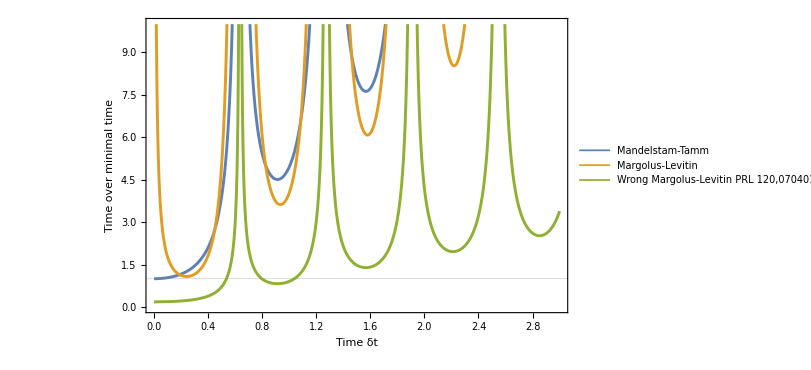

```mathematica
δt=.;
dim=31;
H=DiagonalMatrix[RandomReal[{-1,1},{dim}]0+Table[Tan[n/(dim+0.0001)π/2]/20000,{n,1,dim}]];

H=H-DiagonalMatrix[ConstantArray[Min[Eigenvalues[H]],{dim}]];

psi0=Normalize[RandomReal[{-1,1},{dim}]+ⅈ RandomReal[{-1,1},{dim}]];
psi0=Normalize[Exp[ⅈ RandomReal[{0,2π},{dim}]]];
psi=MatrixExp[-ⅈ H δt].psi0;

Bures=ArcCos[Abs[Conjugate[psi0].psi]];

H1=Re[Conjugate[psi0].(H).psi0];
H2=Re[Conjugate[psi0].(H.H).psi0];
H3=Re[Conjugate[psi0].(H.H.H).psi0];
H4=Re[Conjugate[psi0].(H.H.H.H).psi0];
H5=Re[Conjugate[psi0].(H.H.H.H.H).psi0];
H6=Re[Conjugate[psi0].(H.H.H.H.H.H).psi0];
ΔH=√(H2-H1^2)
H1
ΔH/H1
Plot[{δt/(Bures/ΔH),δt/((Bures/(π/2))Bures/H1),δt/(Bures/H1)(* Definition in PRL 120,070401 (2018) *)},{δt,10^-5,3},GridLines->{{},{1}},PlotRange->{0,10},FrameLabel->{"Time δt","Time over minimal time"},PlotLegends->{"Mandelstam-Tamm","Margolus-Levitin","Wrong Margolus-Levitin PRL 120,070401 (2018)"}]
```

## Pure states

4.80468

6.66331

0.721064

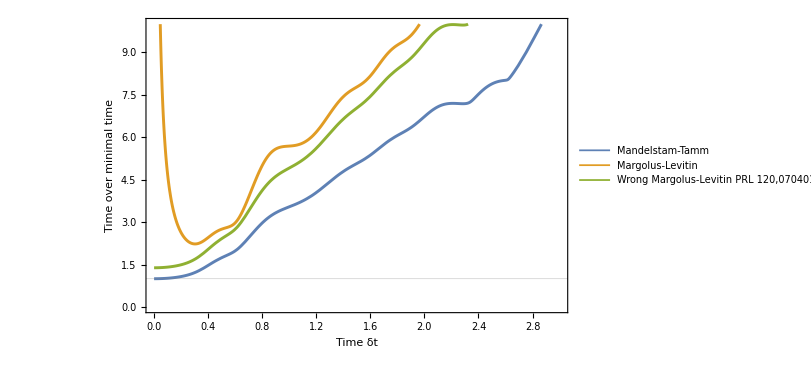

```mathematica
δt=.;
dim=35;
H=DiagonalMatrix[RandomReal[{-1,1},{dim}]10+0Table[n+1/2,{n,0,dim-1}]];

H=H-DiagonalMatrix[ConstantArray[Min[Eigenvalues[H]],{dim}]];

psi0=Normalize[RandomReal[{-1,1},{dim}]+ⅈ RandomReal[{-1,1},{dim}]];
psi=MatrixExp[-ⅈ H δt].psi0;

Bures=ArcCos[Abs[Conjugate[psi0].psi]];

H1=Re[Conjugate[psi0].(H).psi0];
H2=Re[Conjugate[psi0].(H.H).psi0];
H3=Re[Conjugate[psi0].(H.H.H).psi0];
H4=Re[Conjugate[psi0].(H.H.H.H).psi0];
H5=Re[Conjugate[psi0].(H.H.H.H.H).psi0];
H6=Re[Conjugate[psi0].(H.H.H.H.H.H).psi0];
ΔH=√(H2-H1^2)
H1
ΔH/H1
Plot[{δt/(Bures/ΔH),δt/((Bures/(π/2))Bures/H1),δt/(Bures/H1)(* Definition in PRL 120,070401 (2018) *)},{δt,10^-5,3},GridLines->{{},{1}},PlotRange->{0,10},FrameLabel->{"Time δt","Time over minimal time"},PlotLegends->{"Mandelstam-Tamm","Margolus-Levitin","Wrong Margolus-Levitin PRL 120,070401 (2018)"}]
```

## Numerical tests of analytical proof above

```mathematica
δt=0.000004;

A=Transpose[{psi0}].Conjugate[{psi0}];
ΔA=√(Conjugate[psi].(A.A).psi-(Conjugate[psi].(A).psi)^2);

vec1=A.psi-(Conjugate[psi].(A.psi))psi;

vec2=H.psi-(Conjugate[psi].(H.psi))psi;

Chop[ΔA]/(δt ΔH)

(* The two vetors are parallel, saturating the Cauchy-Schwarz inequality *)
t1=Norm[1/ΔA(vec1-(Conjugate[vec2].vec1)/ΔH^2 vec2)]
t2=Norm[1/ΔH(vec2-(Conjugate[vec1].vec2)/ΔA^2 vec1)]

t3=√(((-H1^6+2 H1^3 H3-H3^2-3 H1^4 ΔH^2+2 H1 H3 ΔH^2+H4 ΔH^2-3 H1^2 ΔH^4-ΔH^6) δt^2)/(4 ΔH^4))

t1/t3
t2/t3
```

1.

9.0889×10^-6

9.09567×10^-6

9.0889×10^-6

1.

1.00074

```mathematica
δt1=δt=0.01;
A1=(Conjugate[psi].psi0)(Conjugate[psi0].psi);
δt2=δt=δt+0.0000001;
A2=(Conjugate[psi].psi0)(Conjugate[psi0].psi);

A=Transpose[{psi0}].Conjugate[{psi0}];
ΔA=√(Conjugate[psi].(A.A).psi-(Conjugate[psi].(A).psi)^2);

Chop[((A1-A2)/(δt2-δt1))/(2ΔA ΔH)]
```

0.999731

```mathematica
δt1=δt=0.01;
A1=(Conjugate[psi].psi0)(Conjugate[psi0].psi);
δt2=δt=δt+0.000001;
A2=(Conjugate[psi].psi0)(Conjugate[psi0].psi);
Chop[((A1-A2)/(δt2-δt1))/(2 √(A2(1-A2)))1/ΔH]
```

0.999686

```mathematica
Chop[ArcCos[√((Conjugate[psi].psi0)(Conjugate[psi0].psi))]/δt 1/ΔH]
```

0.999912

## Statistical mixtures

{0.00001,2.83849}

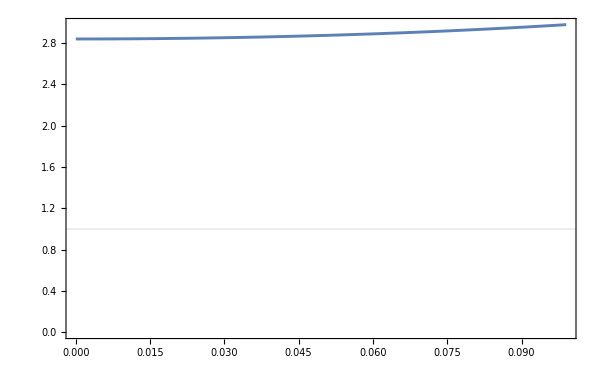

```mathematica
dim=15;

ρ0=DiagonalMatrix[(#/Total[#])&@RandomReal[{0,1},{dim}]];

(*ρ0=ConstantArray[0,{dim,dim}];
ρ0⟦5,5⟧=0.5;
ρ0⟦6,6⟧=0.5;
*)

hermitian=RandomReal[{-1,1},{dim,dim}]+ⅈ RandomReal[{-1,1},{dim,dim}];
unitary=MatrixExp[-ⅈ ( DiagonalMatrix[RandomReal[{-1,1},{dim}]]+UpperTriangularize[hermitian,1]+
ConjugateTranspose[UpperTriangularize[hermitian,1]])];

H=unitary.DiagonalMatrix[RandomReal[{-1,1},{dim}]10+0Table[n+1/2,{n,0,dim-1}]].ConjugateTranspose[unitary];

ΔH=Re[√(Tr[ρ0.H.H]-Tr[ρ0.H]^2)];

tab=Table[
ρ=MatrixExp[-ⅈ H δt].ρ0.MatrixExp[ⅈ H δt];

(*
e=Eigensystem[ρ];
Re[Total[(Eigenvalues[Simplify[Transpose[e⟦2⟧].DiagonalMatrix[√e⟦1⟧].Conjugate[e⟦2⟧]].ρ0.Simplify[Transpose[e⟦2⟧].DiagonalMatrix[√e⟦1⟧].Conjugate[e⟦2⟧]]]
)^(1/2)]]*)

{δt,δt/(ArcCos[Abs[Re[Total[√Eigenvalues[√ρ0 .ρ.√ρ0]]]]]/ΔH)},{δt,10^-5,0.1,1. 10^-3}];

tab⟦1⟧

ListPlot[tab,GridLines->{{},{1}},PlotRange->{0,All}]
```

## Coherent states

```mathematica
IsPositiveQ[ϵ]^=True;
IsNumericQ[ϵ]^=True;
IsPositiveQ[δx]^=True;
IsNumericQ[δx]^=True;
IsNumericQ[λ]^=True;
IsPositiveQ[λ]^=True;
IsPositiveQ[τ]^=True;
IsNumericQ[τ]^=True;
```

```mathematica
δα:=δx/(√((2 hbar)/(m ω)))+ⅈ δp/(√(2 hbar m ω));
Bures=Simplify[(Series[(Simplify[Series[Simplify[ArcCos[1-ϵ]],{ϵ,0,10}],{ϵ>0}]//Normal)/.ϵ->Simplify[Series[Simplify[1-Exp[-ϵ^2/2]],{ϵ,0,10}],{ϵ>0}]//Normal,{ϵ,0,1}]//Normal)/.ϵ->Simplify[√((δα/.δp->-δp)δα)]]
(*Simplify[Normal[Series[Simplify[ArcCos[Exp[-ϵ^2]]],{ϵ,0,5}],{ϵ>0}]]*)

Bures/.δp->0
```

(√((δp^2+m^2 δx^2 ω^2)/(hbar m ω)))/(√2)

(δx √((m ω)/hbar))/(√2)

```mathematica
Solve[Normal[Series[U0/2(1-Cos[(4π)/λ x]),{x,0,2}]]==1/2 m ω^2 x^2,U0]⟦1⟧
```

{U0→(m λ^2 ω^2)/(8 π^2)}

```mathematica
ΔE=(D[U0/2(1-Cos[(4π)/λ x]),x]/.x->λ/8)√(hbar/(2m ω));
Assuming[{hbar>0,ω>0,m>0},FullSimplify[(hbar (Bures/.{δx->λ/2,δp->0}))/ΔE/.U0->1/8 m λ^2 ω^2]]/.ω->(2π)/Subscript[τ, HO]
```

τ_HO/π^2

```mathematica
Subscript[τ, QSL]/.Solve[Assuming[{hbar>0,ω>0,m>0},FullSimplify[(hbar (Bures/.{δx->0,δp->m (2λ)/Subscript[τ, QSL]}))/ΔE/.U0->1/8 m λ^2 ω^2/.ω->(2π)/Subscript[τ, HO]]]==Subscript[τ, QSL],Subscript[τ, QSL]]⟦4⟧
```

(√2 τ_HO)/π^(3/2)

```mathematica
N[{Subscript[τ, HO]/π^2,(√2 Subscript[τ, HO])/π^(3/2)}]
```

{0.101321 τ_HO,0.253975 τ_HO}